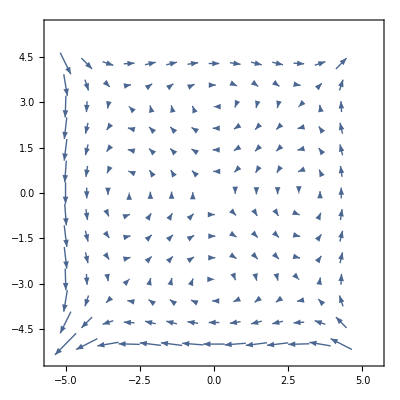

```mathematica
F[x_,y_]:={y^3-9y, x^3-9x}
VectorPlot[F[x,y],{x,-5,5},{y,-5,5}]
```

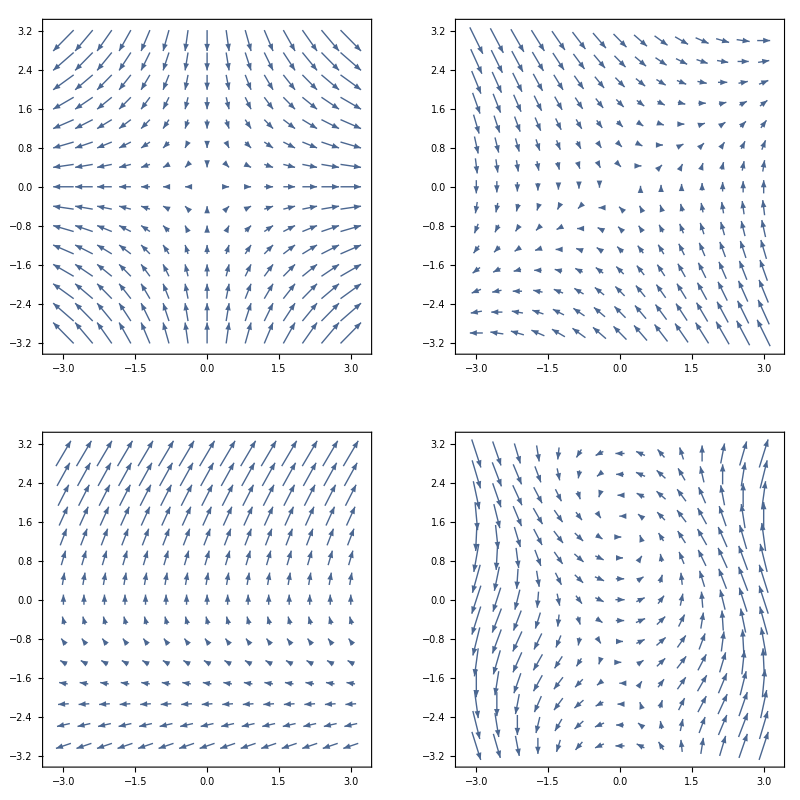

```mathematica
GraphicsGrid[{{VectorPlot[{x,-y},{x,-3,3},{y,-3,3}],VectorPlot[{y,x-y},{x,-3,3},{y,-3,3}]},{VectorPlot[{y,y+2},{x,-3,3},{y,-3,3}],VectorPlot[{Cos[x+y],x},{x,-3,3},{y,-3,3}]}}]
```

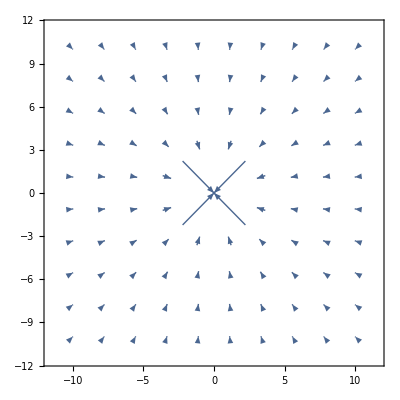

```mathematica
Clear[x]
Clear[y]
ϵ=9 10^9;
q=-2 10^-5;
Q=5 10^-5;
m=9 10^-2;
Subscript[x, 0]=10;
Subscript[y, 0]=-10;
Subscript[vx, 0]=0;
Subscript[vy, 0]=0;
maxT=5.8;
F[r_?ListQ]:= (ϵ q Q)/Norm[r]^3 r
vecPlot =VectorPlot[F[{x,y}],{x,-10,10},{y,-10,10},VectorPoints->10]
(*VectorPlot[F[{x,y}],{x,y}∈ParametricRegion[{x,y},1≤x^2+y^2,{{x,-10,10},{y,-10,10}}]]
StreamPlot[F[{x,y}],{x,-2,2},{y,-2,2}]*)
(*sol = NDSolveValue[{
x'[t]==vx[t],
vx'[t]==(F[{x[t],y[t]}][[1]])/m,
y'[t]==vy[t],
vy'[t]==(F[{x[t],y[t]}][[2]])/m,
x[0]==Subscript[x, 0],vx[0]==Subscript[vx, 0],y[0]==Subscript[y, 0],vy[0]==Subscript[vy, 0]}, 
{x,vx,y,vy},
{t,0,maxT}];*)
sol = NDSolveValue[{
x'[t]==vx[t],
vx'[t]==(F[{x[t],y[t]}]⟦1⟧)/m,
y'[t]==vy[t],
vy'[t]==(F[{x[t],y[t]}]⟦2⟧)/m  ,
x[0]==Subscript[x, 0],vx[0]==Subscript[vx, 0],y[0]==Subscript[y, 0],vy[0]==Subscript[vy, 0]}, 
{x,vx,y,vy},
{t,0,maxT}];
x:=sol[[1]];
y:=sol[[3]];

Animate[
Show[vecPlot,Graphics[Circle[{x[t],y[t]},0.3]]],
{t,0,maxT,0.001}
]
```